```mathematica
ecs={x''[t]==0,y''[t]==-9.8}; (*ecuacion que indica que la aceleracion es 0*)
cin={x[0]==x0,y[0]==y0,x'[0]==v0 Cos[θ0],y'[0]==v0 Sin[θ0]}; (*Posicion inicial, y luego la velocidad inicial, separada en sus dos componentes, se separa por angulo, por tanto depende del angulo inicial*)
```

* WhenEvent [evento, accion] Especifica que <accion > ocurre cuando se cumple cierto < evento > el cual se define como una igualdad en una ecuacion

```mathematica
eventos={WhenEvent[y[t]==1,y'[t]->-y'[t]],WhenEvent[x[t]==1,x'[t]->-x'[t]],WhenEvent[y[t]==0,y'[t]->-y'[t]],WhenEvent[x[t]==0,x'[t]->-x'[t]]};
```

* Por ejemplo en el codigo de arriba, que es una listga de WhenEvent, los WhenEvent son los siguientes:
	1) WhenEvent[y[t]==1,y’[t]->-y’[t]]
		Cuando la posicion y es igual a 1, entonces la derivada de y (la velocidad y) se convierte en menos derivada de y (- velocidad y), el equivalente de rebotar luego de alcanzar la altura 1 (ojo que no 				modifica la velocidad x)		
	2) WhenEvent[x[t]==1,x’[t]->-x’[t]]
		Igual que el evento de arriba; cuando la posicion de x es igual a 1, la velocidad que llevaba se vuelve negativa, el equivalente de rebotar
	3) WhenEvent[y[t]==0,y’[t]->-y’[t]]
		Cuando la posicion de y es 0, rebota
	4) WhenEvent[x[t]==0,x’[t]->-x’[t]]
		Cuando la posicion de x es 0, rebota

En el siguiente codigo, se crea una funcion la cual resuelve las ecuaciones  de movimiento (que es obtener la posicion (x,y) en un momento (t) dado, osea que t es la variable independiente)
La funcion pide de variables iniciales la posicion x inicial, la posicion y inicial, la velocidad inicial y el angulo inicial.

```mathematica
sol[x00_,y00_,v00_,θ00_]:=First@NDSolve[Join[ecs,cin,eventos]/.{x0->x00,y0->y00,v0->v00,θ0->θ00},{x[t],y[t]},{t,0,10}]
```

> First@NDSolve extrae la solucion a la forma que vemos mas abajo en el Out, ya que NDSolve suele entregar {{solucion}} entre llaves
> NDSolve[eqs,u,{t,to,tf}] toma en su interior:
	eqs -> la cual es una lista de ecuaciones (llamesele condiciones)
	u -> variables dependientes, en este caso:
		x[t] e y[t]
	{t,to,tf} -> (exclusivo para NDSolve, ya que es una solucion numerica, se le da un rango a la variable t) que va de t inicial (to) a t final (tf)
> Join[ecs,cin,eventos] une en una lista mas larga las: (ya que en NDSolve, pide una lista de ecuaciones, se las entregamos juntas en una sola lista)
	Que contiene cada ecuacion en este caso? lo siguiente:
		ecs -> condiciones iniciales (que la segunda derivada de x e y sean 0, osea que no hay aceleracion)
		cin -> son las ecuaciones cineticas, escenciales para despejar la posicion a partir de los datos y otras condiciones (x[t] = xo + t*x’[t]+ (1/2)*t^2*x’’[t] para <x>, hacer lo mismo para <y> )
		eventos -> es una lista de WhenEvents de que se debe hacer cuando un valor vale tanto
	>>NDSolve va time step por time step (dt), cuando avanza (su avance es dictado por las ecuaciones o condiciones ecs y cin) comprueba si esta ante un WhenEvent, cuando choca por asi decirlo
	con uno de restos eventos, realiza la accion, que en este caso es cambiar de signo la velocidad (para todos, pero en diferentes condiciones), ahora con la accion tomada, (la velocidad ahora
	con signo contrario) se continuan los time-steps (dt)	
>Se utiliza /. para aplicar los parametros a las variables internas (las cuales depende de x0, y0, v0, angulo)

```mathematica
solu=sol[0,0,10,25°] (*calculemos lo que sucede con estas condiciones iniciales, pos inicial (0,0), velocidad es 10 y angulo es 25*)
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}

Arriba la solucion en forma de funcion interpolada, la cual podemos observar con Plot Parametrico, el que entrega la linea que siguen las funciones

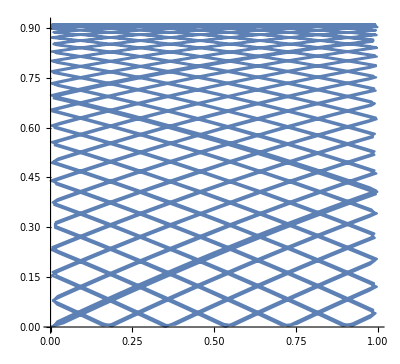

```mathematica
ParametricPlot[{x[t],y[t]}/.solu,{t,0,10}] (*/. hace que se le aplica cada solucion a la lista {x[t],y[t]} las cuales para el ParametricPlot son fx y fy*)
```

```mathematica
solucion[x00_,y00_,v00_,θ00_]:=Module[{},solu=First@NDSolve[Join[ecs,cin,eventos]/.{x0->x00,y0->y00,v0->v00,θ0->θ00},{x[t],y[t]},{t,0,10}]]
```

```mathematica
Manipulate[ParametricPlot[{x[t],y[t]}/.solucion[0,0,v00,θ00],{t,0,10}],{v00,0,10,.1},{θ00,0,2π,.1}]
```

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {x''[0.000204082]==0,y''[0.000204082]==-9.8,x[0]==0,y[0]==0,x'[0]==0,y'[0]==0,WhenEvent[y[t]==1,y'[t]→-y'[t]],WhenEvent[x[t]==1,x'[t]→-x'[t]],WhenEvent[y[t]==0,y'[t]→-y'[t]],WhenEvent[x[t]==0,x'[t]→-x'[t]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x''[0.000204082]==0.,y''[0.000204082]==-9.8,x[0.]==0.,y[0.]==0.,x'[0.]==0.,y'[0.]==0.,WhenEvent[y[t]==1.,y'[t]→-1. y'[t]],WhenEvent[x[t]==1.,x'[t]→-1. x'[t]],WhenEvent[y[t]==0.,y'[t]→-1. y'[t]],WhenEvent[x[t]==0.,x'[t]→-1. x'[t]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: {x''[0.204286]==0,y''[0.204286]==-9.8,x[0]==0,y[0]==0,x'[0]==0,y'[0]==0,WhenEvent[y[t]==1,y'[t]→-y'[t]],WhenEvent[x[t]==1,x'[t]→-x'[t]],WhenEvent[y[t]==0,y'[t]→-y'[t]],WhenEvent[x[t]==0,x'[t]→-x'[t]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408367 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

```mathematica
g=-9.8;
```

```mathematica
ecs={x''[t]==0,y''[t]==g};
cin[x0_,y0_,v0_,θ0_]={x[0]==x0,y[0]==y0,x'[0]==v0 Cos[θ0],y'[0]==v0 Sin[θ0]};
```

```mathematica
eventos[dpared_]={WhenEvent[y[t]==0,y'[t]->-y'[t]],WhenEvent[x[t]==dpared,x'[t]->-x'[t]],WhenEvent[x[t]==0,Tend0=t;"StopIntegration"]}
```

{WhenEvent[y[t]==0,y'[t]→-y'[t]],WhenEvent[x[t]==dpared,x'[t]→-x'[t]],WhenEvent[x[t]==0,Tend0=t;StopIntegration]}

```mathematica
sol[x0_,y0_,v0_,θ0_,xpared_]:=First@NDSolve[Join[ecs,cin[x0,y0,v0,θ0],eventos[xpared]],{x[t],y[t]},{t,0,10}]
```

```mathematica
solu=sol[0,1.5,5,-30°,3]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}

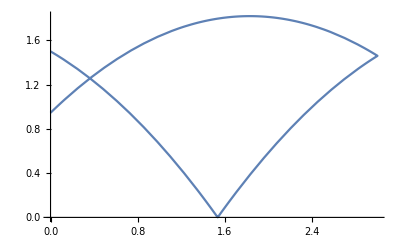

```mathematica
ParametricPlot[{x[t],y[t]}/.solu,{t,0,Tend0}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
solucion[x0_,y0_,v0_,θ0_,xpared_]:=Module[{},solu=First@NDSolve[Join[ecs,cin[x0,y0,v0,θ0],eventos[xpared]],{x[t],y[t]},{t,0,10}];ParametricPlot[{x[t],y[t]}/.solu,{t,0,Tend0},PlotRange->{{0,5},{0,2.5}}]]
```

```mathematica
Manipulate[Evaluate@solucion[p[[1]],p[[2]],v0,θ °,dispared],{v0,.1,10,.1},{θ,1,89,1},{dispared,2,5,.1},{p,{0,0},{2.5,5}}]
```

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.